## Understanding the distribution of consumers on an implied landscape as a function of both resource availability and temperature limitations.

## Define models at equilibrium

```mathematica
(* Chemostat resource model *)
Imax[T_]:=Exp[-((T-TI)^2)/β];
m[T_]:=Subscript[m, a] Exp[Subscript[m, b] T]+Subscript[m, c];

(* Equation 1 *)
eqC:=CN'[t]==CN[t](e Imax[T] R[t]/(R0+R[t])-m[T]);
```

## Get the equilibria (symbolically)

```mathematica
FullSimplify[Solve[0 == Dil (S-R[t])- Exp[-((T-TI)^2)/β]R[t] CN[t]/(R0+R[t]), 0 == CN[t](e Exp[-((T-TI)^2)/β] R[t]/(R0+R[t])-Subscript[m, a] Exp[Subscript[m, b] T]+Subscript[m, c])]]
```

Solve::ivar: 0==CN[t] (0.05-0.01 ⅇ^(0.1 T)+(0.5 ⅇ^(-1/150 Plus[«2»]^2) R[t])/(2+R[t])) is not a valid variable.

Solve[R[t]+(ⅇ^(-1/150 (-25+T)^2) CN[t] R[t])/(2+R[t])==1,CN[t] (0.05-0.01 ⅇ^(0.1 T)+(0.5 ⅇ^(-1/150 (-25+T)^2) R[t])/(2+R[t]))==0]

## Define standard values of the system

```mathematica
R0=0.5;
e=0.5;
TI=25;
β=150;
Subscript[m, a]=0.01;
Subscript[m, b]=0.1;
Subscript[m, c]=0.05;
uppertval=40
```

40

## Get the equilibrium values and the eigenvalues (assuming chemostat)

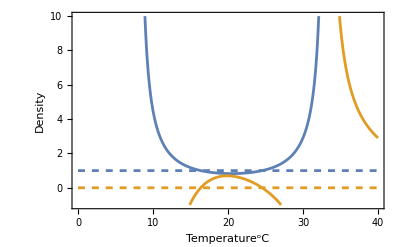
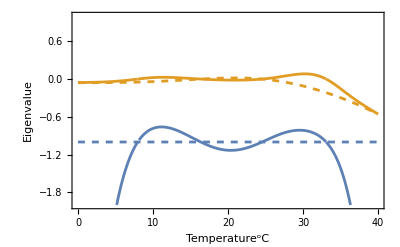

```mathematica
(* Define parameters and equations for the chemostat model *)
Dil=1;
S=1;
R0=2;

eqR:=R'[t]==Dil (S-R[t])- Imax[T]R[t] CN[t]/(R0+R[t]);
eqsol=Solve[{eqR[[2]]==0,eqC[[2]]==0},{R[t],CN[t]}];
eigenvals=Eigenvalues[{{D[eqR[[2]],R[t]],D[eqR[[2]],CN[t]]},{D[eqC[[2]],R[t]],D[eqC[[2]],CN[t]]}}];

Row@{Show[Plot[Evaluate[{R[t],CN[t]}/.eqsol[[2]]],{T,0,uppertval},PlotRange->{-1,10},ImageSize->400,Frame->{True,True,False,False},FrameLabel->{"Temperature^oC","Density"},LabelStyle->13],Plot[Evaluate[{R[t],CN[t]}/.eqsol[[1]]],{T,0,uppertval},PlotRange->{-1,10},PlotStyle->Dashed]],
Show[Plot[Evaluate[eigenvals/.eqsol[[2]]],{T,0,uppertval},PlotRange->{-2Dil,1},ImageSize->400,Frame->{True,True,False,False},FrameLabel->{"Temperature^oC","Eigenvalue"},LabelStyle->13],
Plot[Evaluate[eigenvals/.eqsol[[1]]],{T,0,uppertval},PlotRange->{-Dil-.5,1},PlotStyle->Dashed]]}

(* Blue lines are resource dynamics and orange are consumers, dashed represents (S,0) equilibrium and solid lines are non trivial eqilibrium*)
(* Right panels: Solid lines shows the eigenvalues (blue and orange are #1 and #2) for the non trivial equilibrim and dahsed for the (S,0) equilibrium *)
```

```mathematica
FullSimplify[Solve[0 == Dil (S-R[t])- Exp[-((T-TI)^2)/β]R[t] CN[t]/(R0+R[t]), 0 == CN[t](e Exp[-((T-TI)^2)/β] R[t]/(R0+R[t])-Subscript[m, a] Exp[Subscript[m, b] T]+Subscript[m, c])]]
```

Solve::ivar: 0==CN[t] (0.05-0.01 ⅇ^(0.1 T)+(0.5 ⅇ^(-1/150 Plus[«2»]^2) R[t])/(2+R[t])) is not a valid variable.

Solve[R[t]+(ⅇ^(-1/150 (-25+T)^2) CN[t] R[t])/(2+R[t])==1,CN[t] (0.05-0.01 ⅇ^(0.1 T)+(0.5 ⅇ^(-1/150 (-25+T)^2) R[t])/(2+R[t]))==0]